# Constrained method

## Start

```mathematica
SetOptions[InputNotebook[],AutoGeneratedPackage->Automatic]
```

```mathematica
packageDirectory=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"*"}];
$Path=Join[$Path,FileNames[packageDirectory]];
```

```mathematica
<<"pyramid1d`"
<<"pyramidalCyclope1D`"
```

```mathematica
noteBookMode="ConstrainedNewMethod";
```

## Test Points {line1, line2, pyrf12}

```mathematica
dis=1;
```

```mathematica
(* We create test points for compilation test *)
line1=GaussianFilter[Table[If[11<= p<=18,1,0],{p,1,30}],1];
line2=GaussianFilter[Table[If[11<= p<=18,1,0],{p,1-dis,30-dis}],1];
ListPlot[{line1, line2},Joined->True,PlotMarkers->Automatic,PlotRange->All,PlotLabel->"Test Points",PlotLegends->{"ia","ib"}];
```

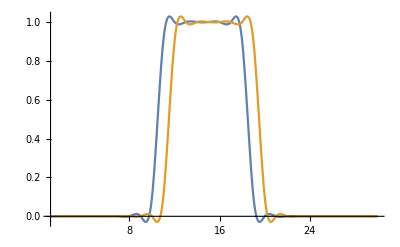

```mathematica
(*generate functions of pyramid with pyrFuncGen*)
(* input-> {original points, number of levels}*)
(* Output-> {functions f and df for n+1 levels} *)
pyrf1=pyrFuncGen[line1,4];
pyrf2=pyrFuncGen[line2,4];
pyrf12=Flatten[{pyrf1, pyrf2}, {{2},{1},{3}}];

Plot[{pyrf12[[1,1,1]][x],pyrf12[[1,2,1]][x]},{x,1,30}]
```

## Pyramidal Flow 1D (PyrFlow1D)

### PyrUpgrade1D

```mathematica
(* Function to update values of v1 and v2 with Over Constrained standards *)
(* Any value that does not meets the constraints becomes 0 *)

(* Input-> {{initial values for v1, v2 and status, and counter e}, pixel of interest, {functions f1, df1, f2, df2}, threshold for magnitude error}*)
(* Output-> {new values for v1, v2 and status and e} *)
PyrUpgrade1D[{v1_,v2_,status_,e_},p0_, {{fline1_,dfline1_} ,{fline2_,dfline2_}}, threshold_,n_,"ConstrainedNewMethod"]:=Block[{fric1,fric2,p1, p2, c,d1,d2,dv1,dv2},(

p1=p0-v1;
p2=p0+v2;

c = (fline1[p0]+fline2[p0])/2;
d1=dfline1[p1];
d2=dfline2[p2];

fric1=3*dfline1'[p1];
fric2=3*dfline2'[p2];

(* d1 and d2 have to be the same sign in every iteration *)
If[d1*d2 <0, If[e<=n,Return[{v1,v2,"oksign",e+1}],Return[{0.,0.,"sign",e}]]];

(* magnitud *)
If[(Abs[d1]<threshold||Abs[d2]<threshold ),If[e<=n,Return[{v1,v2,"okmag",e+1}],Return[{0.,0.,"mag",e}]]];

(* Change of sign during iteration *)
(*If[(dfline1[p0]*d1<0||dfline2[p0]*d2<0),If[e<2,Return[{v1,v2,"flip",e+1}],Return[{0.,0.,"flip",e}]]];*)

(* dv1,dv2 : step from last {v1,v2} to new {v1,v2} *)
{dv1,dv2}= {(fline1[p1]-c)/(d1+Sign[d1]*Abs[fric1]),(c-fline2[p2])/(d2+Sign[d2]*Abs[fric2])};

If[e<=n,{v1+dv1,v2+dv2,If[Norm[{dv1,dv2}]<0.01,"converged","ok"],e},Return[{0.,0.,status,e}]]

)];

(* No other solution will be calculated when status records an error message in this pyramidal level*)
(* status: "OK" -> solution respects constraints,  errors: "sign", "mag", "flip" *)
(* status: "converged" -> we converged!! *)
PyrUpgrade1D[{v1_,v2_,"sign",e_},p0_, {{fline1_,dfline1_} ,{fline2_,dfline2_}}, threshold_,n_,"ConstrainedNewMethod"]:=Return[{v1,v2,"sign",e}];

PyrUpgrade1D[{v1_,v2_,"mag",e_},p0_, {{fline1_,dfline1_} ,{fline2_,dfline2_}}, threshold_,n_,"ConstrainedNewMethod"]:=Return[{v1,v2,"mag",e}];

PyrUpgrade1D[{v1_,v2_,"flip",e_},p0_, {{fline1_,dfline1_} ,{fline2_,dfline2_}}, threshold_,n_,"ConstrainedNewMethod"]:=Return[{v1,v2,"flip",e}];
```

### Test

```mathematica
(* initial values *)
{v1, v2,status,e}={0.5,3,"ok",0.};
i=0;
p=12;
```

```mathematica
n=1;
status="ok";
```

```mathematica
(*Test for PyrUpgrade1D, manual test to iterate multiple times*)
(* n is the level of pyramid *)

{v1,v2,status,e}=PyrUpgrade1D[{v1,v2,status,e},p, pyrf12[[n]],0.01,1,noteBookMode]
```

{0.,0.,sign,1.}

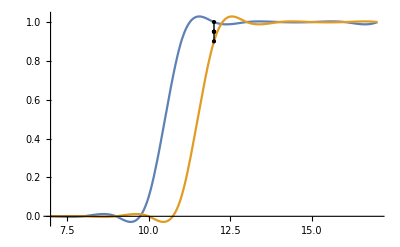

```mathematica
(* see *)
seePlot[p,5,{v1,v2},pyrf12[[n]]]
```

### PyrFlow1D

```mathematica
(* This will only give values that sum up to the magnitude of v 
Or if v0 = 0, random values between 10 and -10 *)
(*n=allowed failed levels, u= shift on v solution through levels*)

newValues[i_,n_,u_,{v1_,v2_,status_,e_},newv0_,"ConstrainedNewMethod"]:=Block[{v,r,rs,newVals},(
v=v1+v2;

If[e>n,
Return[{{0.,0.}}];
];

If[v≠0. && status=="ok",
newVals=Table[
r=RandomReal[];
{r,1-r}*v
,{j,i}];
If[u≠0.,Join[newVals,newVals-u, newVals+u],newVals]

,
newv0
]

)]
```

```mathematica
(* We create the list of values in case v=0 *)
r=RandomReal[];
rangev0=Range[0,5,0.2];

newv0=Join[{r,1-r}*#&/@rangev0,{1-r,r}*#&/@rangev0,{1,0}*#&/@rangev0,{0,1}*#&/@rangev0]
```

{{0.,0.},{0.095158,0.104842},{0.190316,0.209684},{0.285474,0.314526},{0.380632,0.419368},{0.47579,0.52421},{0.570948,0.629052},{0.666106,0.733894},{0.761264,0.838736},{0.856422,0.943578},{0.95158,1.04842},{1.04674,1.15326},{1.1419,1.2581},{1.23705,1.36295},{1.33221,1.46779},{1.42737,1.57263},{1.52253,1.67747},{1.61769,1.78231},{1.71284,1.88716},{1.808,1.992},{1.90316,2.09684},{1.99832,2.20168},{2.09348,2.30652},{2.18863,2.41137},{2.28379,2.51621},{2.37895,2.62105},{0.,0.},{0.104842,0.095158},{0.209684,0.190316},{0.314526,0.285474},{0.419368,0.380632},{0.52421,0.47579},{0.629052,0.570948},{0.733894,0.666106},{0.838736,0.761264},{0.943578,0.856422},{1.04842,0.95158},{1.15326,1.04674},{1.2581,1.1419},{1.36295,1.23705},{1.46779,1.33221},{1.57263,1.42737},{1.67747,1.52253},{1.78231,1.61769},{1.88716,1.71284},{1.992,1.808},{2.09684,1.90316},{2.20168,1.99832},{2.30652,2.09348},{2.41137,2.18863},{2.51621,2.28379},{2.62105,2.37895},{0.,0.},{0.2,0.},{0.4,0.},{0.6,0.},{0.8,0.},{1.,0.},{1.2,0.},{1.4,0.},{1.6,0.},{1.8,0.},{2.,0.},{2.2,0.},{2.4,0.},{2.6,0.},{2.8,0.},{3.,0.},{3.2,0.},{3.4,0.},{3.6,0.},{3.8,0.},{4.,0.},{4.2,0.},{4.4,0.},{4.6,0.},{4.8,0.},{5.,0.},{0.,0.},{0.,0.2},{0.,0.4},{0.,0.6},{0.,0.8},{0.,1.},{0.,1.2},{0.,1.4},{0.,1.6},{0.,1.8},{0.,2.},{0.,2.2},{0.,2.4},{0.,2.6},{0.,2.8},{0.,3.},{0.,3.2},{0.,3.4},{0.,3.6},{0.,3.8},{0.,4.},{0.,4.2},{0.,4.4},{0.,4.6},{0.,4.8},{0.,5.}}

```mathematica
nV=newValues[10,1,0.25,{-1,-1.,"ok",1.},newv0,"ConstrainedNewMethod"]
Total/@nV
```

{{-0.498038,-1.50196},{-0.238346,-1.76165},{-1.5008,-0.4992},{-1.754,-0.245999},{-0.172973,-1.82703},{-0.817947,-1.18205},{-0.00988018,-1.99012},{-1.25603,-0.743972},{-0.36984,-1.63016},{-0.415861,-1.58414},{-0.748038,-1.75196},{-0.488346,-2.01165},{-1.7508,-0.7492},{-2.004,-0.495999},{-0.422973,-2.07703},{-1.06795,-1.43205},{-0.25988,-2.24012},{-1.50603,-0.993972},{-0.61984,-1.88016},{-0.665861,-1.83414},{-0.248038,-1.25196},{0.0116542,-1.51165},{-1.2508,-0.2492},{-1.504,0.00400134},{0.0770267,-1.57703},{-0.567947,-0.932053},{0.24012,-1.74012},{-1.00603,-0.493972},{-0.11984,-1.38016},{-0.165861,-1.33414}}

{-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.5,-2.5,-2.5,-2.5,-2.5,-2.5,-2.5,-2.5,-2.5,-2.5,-1.5,-1.5,-1.5,-1.5,-1.5,-1.5,-1.5,-1.5,-1.5,-1.5}

```mathematica
(* This will give back a value that converged or is on "ok" status. If not, error is returned and {v1,v2} goes back to 0. *)

pickNewValue[tableNewVals_,condition_,"ConstrainedNewMethod"]:=Block[{newValOk,newValCon,newValAny,noFakeConverge},(

(* Criterias to select a solution *)
newValCon=Select[tableNewVals,(#[[3]]=="converged")&&condition[#]&,1];
newValAny=Select[tableNewVals,(#[[3]]≠ "ok"&&#[[3]]≠ "oksign"&&#[[3]]≠ "okmag"&&#[[3]]≠ "converged")&&condition[#]&,1];
newValOk=Select[tableNewVals,(#[[3]]=="ok"||#[[3]]=="oksign"||#[[3]]=="okmag")&& condition[#]&,1];

noFakeConverge=Select[tableNewVals,(#[[3]]≠ "ok"&&#[[3]]≠ "oksign"&&#[[3]]≠ "okmag"&&#[[3]]≠ "converged")&,1];

(* No solution meets criteria *)
If[newValCon=={}&&newValAny=={}&&newValOk=={},

If[noFakeConverge=={},
Flatten[{0.,0.,"fakeconverged",tableNewVals[[1,4]]+1}]
,
Flatten[{0.,0.,noFakeConverge[[1,3]],noFakeConverge[[1,4]]}]
]

,
(* solution meets criteria but it did not converge *)
If[newValCon=={},
(* solution meets criteria but isn't ok or converged *)
If[newValOk=={},
newValAny[[1]]
,

Flatten[{newValOk[[1,1;;2]],"ok",newValOk[[1,4]]}]
],

newValCon[[1]]
]

]
)]
```

```mathematica
Clear[condition];
condition[x_]:=x[[1]]*x[[2]]>0 && 0<(*Abs[*)Total[x[[1;;2]]](*]*)<1;
```

```mathematica
threshold=0.001;
n=1;
p0=9;
i=10;

updateValues={0.,0.,"ok",1};

(* This will only give values that sum up to the magnitude of v 
Or if v0 = 0, list newv0 is created and fed to the function to try all it's contained values *)

nV=newValues[10,1,0,updateValues[[1;;4]],newv0,"ConstrainedNewMethod"];

tableNV=Table[
tValues=Flatten[{v,updateValues[[3;;4]]}];

Do[
tValues=PyrUpgrade1D[tValues,p0,  pyrf12[[n]],threshold*2^(-n+1),0,noteBookMode]

,{j,1,i}];

tValues
,{v,nV}];

sol=pickNewValue[tableNV,condition,"ConstrainedNewMethod"]
```

{0.,0.,sign,1}

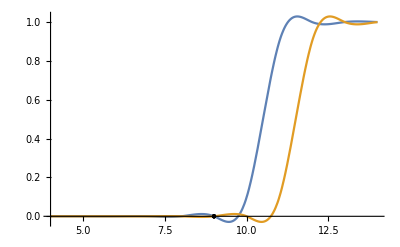

```mathematica
(* see *)
seePlot[p0,5,sol[[1;;2]],pyrf12[[n]]]
```

```mathematica
(* Function to find solutions for all levels of pyramid {l1,l2,l3,l4,...} or {l1} *)
(* Input-> {number of iterations, allowed failed levels, shift on v solution through levels, pixel of interests, pyrfunctions,threshold *)
(* Output-> {v1, v2,status}*)
PyrFlow1D[i_,n_,u_, p0_,listv0_,condition_, pyrfunctions_,threshold_,"ConstrainedNewMethod"]:=Block[{c, updateValues,nV,tableNewValues,tValues},(

c=Length[pyrfunctions]; (* number of levels *)

(*{v1, v2, status, e}*)
updateValues={0.,0.,"ok",0.};

Do[

(* Flag to stop when e≥n *)
If[updateValues[[4]]<=n,updateValues[[3]]="ok", updateValues={0.,0.,updateValues[[3]],updateValues[[4]]}];

(* This will only give values that sum up to the magnitude of v 
Or if v0 = 0, list newv0 is created and fed to the function to try all it's contained values *)
nV=newValues[10,n,u,updateValues[[1;;4]],listv0,"ConstrainedNewMethod"];
(* compute at this scale, using current motion estimate *)

tableNewValues=Table[

(* We initialize whith values calculated at nV and last calculated updateValues[[3;;4]]*)
tValues=Flatten[{v,updateValues[[3;;4]]}];

Do[
tValues=PyrUpgrade1D[tValues,p0, pyrfunctions[[-f]],threshold*2^(-c+1),n,"ConstrainedNewMethod"];
If[tValues[[3]]!="ok",Break[]];

,{j,1,i}];

tValues
,{v,nV}];

(* We only update updateValues with the tValue that converged *)
updateValues=pickNewValue[tableNewValues,condition,"ConstrainedNewMethod"];


c=c-1;
,{f,1,Length[pyrfunctions]}];
updateValues[[1;;3]]
)];
```

#### Test

```mathematica
Clear[condition];
condition[x_]:=x[[1]]*x[[2]]>0 && 0<(*Abs[*)Total[x[[1;;2]]](*]*)<1;
```

```mathematica
p=14;
```

{{0.,0.,sign,1},{0.022432,0.138703,ok,2},{0.,0.,sign,3},{0.0398306,0.0946544,ok,4},{0.,0.,sign,5},{0.0676673,0.0759754,ok,6},{0.0024824,0.0179728,ok,7},{0.250611,0.0386675,ok,8},{0.,0.,sign,9},{0.197292,0.368078,ok,10},{0.,0.,fakeconverged,11},{0.,0.,sign,12},{0.,0.,sign,13},{0.,0.,sign,14},{0.,0.,sign,15},{0.976685,0.00496886,converged,16},{0.,0.,sign,17},{0.385282,0.207473,ok,18},{0.,0.,fakeconverged,19},{0.,0.,sign,20},{0.,0.,sign,21},{0.,0.,sign,22},{0.,0.,sign,23},{0.,0.,sign,24},{0.,0.,sign,25},{0.,0.,sign,26},{0.,0.,sign,27},{0.,0.,sign,28},{0.,0.,sign,29},{0.,0.,sign,30}}

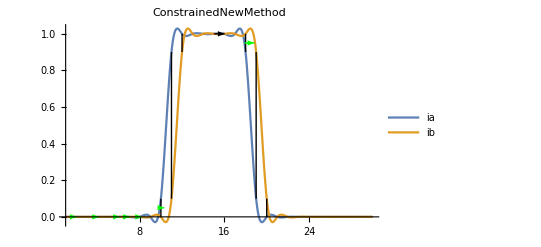

```mathematica
r=RandomReal[];
rangev0=Range[-5,5,0.5];

newv0=Join[{r,1-r}*#&/@rangev0,{1-r,r}*#&/@rangev0,{1,0}*#&/@rangev0,{0,1}*#&/@rangev0];

tes1=lineTest[0,0.02,newv0,condition,Range[1,30],pyrf12[[1;;3]],0.001,noteBookMode]

(* This function is called from pyramidalCyclope1D *)
seeAllLine[0,0.02,newv0,condition,Range[1,30],pyrf12[[1;;2]],0.001,noteBookMode]
```

#### Test

{{0.982857,0.0171424,converged,9},{0.133847,0.811655,ok,10},{0.,0.,fakeconverged,11},{0.,0.,sign,12},{0.,0.,sign,13},{0.,0.,sign,14},{0.,0.,sign,15},{0.976754,0.00648978,converged,16},{0.967825,0.0321746,converged,17},{0.114236,0.837741,converged,18},{0.,0.,fakeconverged,19}}

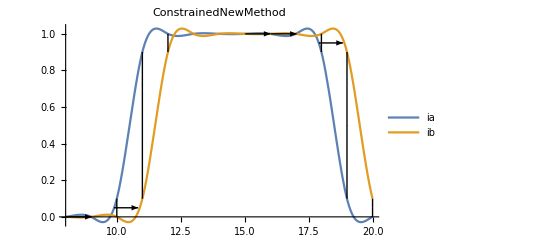

```mathematica
r=RandomReal[];
rangev0=Range[-5,5,0.5];

newv0=Join[{r,1-r}*#&/@rangev0,{1-r,r}*#&/@rangev0,{1,0}*#&/@rangev0,{0,1}*#&/@rangev0];

tes1=lineTest[0,0.1,newv0,condition,Range[p-5,p+5],pyrf12[[1;;4]],0.001,noteBookMode]

(* This function is called from pyramidalCyclope1D *)
seeAllLine[0,0.1,newv0,condition,Range[p-6,p+6],pyrf12[[1;;4]],0.001,noteBookMode]
```

#### Test

0.01*2^(-m) depends on m to update the error depending on the highest resolution scale

```mathematica
{v1, v2,status,e}={0.5,3,"ok",0.};

i=40;
p=15;

(* m-> max lvl, n-> min lvl *)
m=2;
n=2;

(*PyrFlow1D solution*)
{v1,v2,status}=PyrFlow1D[i,1,0.02 ,p,{{0.5,3}},pyrf12[[m;;n]],0.0001*2^(-m+1),noteBookMode]
{Total[{v1,v2}],status}
```

Set::shape: Lists {v1,v2,status} and … are not the same shape.

PyrFlow1D[40,1,0.02,15,{{0.5,3}},{{{InterpolatingFunction[…],InterpolatingFunction[…]},{InterpolatingFunction[…],InterpolatingFunction[…]}}},0.00005,ConstrainedNewMethod]

{3.5,ok}

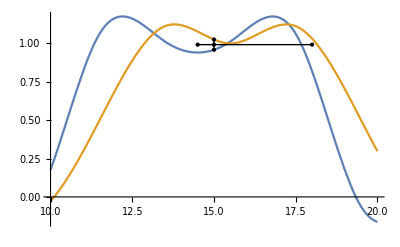

```mathematica
(* see *)
seePlot[p,5,{v1,v2},pyrf12[[m]]]
```

## Graphics for All pixels

### All Pixel Graphics

#### Test

{{0.,0.,sign,1},{0.142542,0.00964268,ok,2},{0.,0.,sign,3},{0.,0.,sign,4},{0.,0.,sign,5},{0.0832046,0.0504963,ok,6},{0.00794833,0.00492877,ok,7},{0.0616306,0.226699,ok,8},{0.,0.,sign,9},{0.219811,0.343877,ok,10},{0.49998,0.500004,converged,11},{0.937276,0.0627244,converged,12},{0.00609028,0.960915,converged,13},{0.,0.,sign,14},{0.,0.,sign,15},{0.,0.,sign,16},{0.,0.,sign,17},{0.368793,0.207233,ok,18},{0.499988,0.499996,converged,19},{0.937275,0.0627249,converged,20},{0.00641285,0.958951,converged,21},{0.,0.,sign,22},{0.950713,0.0492871,converged,23},{0.,0.,sign,24},{0.,0.,sign,25},{0.,0.,sign,26},{0.,0.,sign,27},{0.,0.,sign,28},{0.,0.,sign,29},{0.,0.,sign,30}}

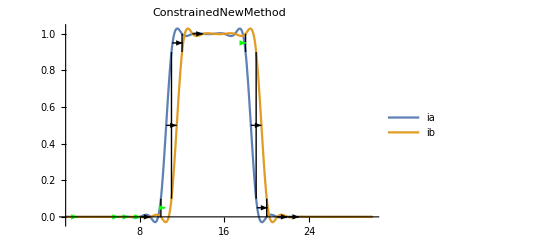

```mathematica
r=RandomReal[];
rangev0=Range[-5,5,0.5];

newv0=Join[{r,1-r}*#&/@rangev0,{1-r,r}*#&/@rangev0,{1,0}*#&/@rangev0,{0,1}*#&/@rangev0];

tes1=lineTest[1,0.02,newv0,condition,Range[1,Length[line1]],pyrf12[[1;;4]],0.001,noteBookMode]

(* This function is called from pyramidalCyclope1D *)
seeAllLine[1,0.02,newv0,condition,Range[1,30],pyrf12[[1;;4]],0.001,noteBookMode]
```

## Graphics for One pixel

```mathematica
pickNewValueIter[tableIterNewVals_,"ConstrainedNewMethod"]:=Block[{newIterValCon,newIterValAny,newIterValOk,noIterFakeConverge},(
newIterValCon=Select[tableIterNewVals,(Last[#][[3]]=="converged"&&Last[#][[1]]*Last[#][[2]]>0 && 0<Last[#][[2]]+Last[#][[1]]<1)&,1];
newIterValAny=Select[tableIterNewVals,((Last[#][[3]]≠ "ok" ||Last[#][[3]]≠ "oksign"||Last[#][[3]]≠ "okmag"||Last[#][[3]]≠ "converged")&&Last[#][[1]]*Last[#][[2]]>0 && 0<Last[#][[2]]+Last[#][[1]]<1)&,1];
newIterValOk=Select[tableIterNewVals,((Last[#][[3]]=="ok" ||Last[#][[3]]=="oksign"||Last[#][[3]]=="okmag")&&Last[#][[1]]*Last[#][[2]]>0 && 0<Last[#][[2]]+Last[#][[1]]<1)&,1];
noIterFakeConverge=Select[tableIterNewVals,(Last[#][[3]]≠ "ok" ||Last[#][[3]]≠ "oksign"||Last[#][[3]]≠ "okmag"||Last[#][[3]]≠ "converged")&,1];

(* No solution meets criteria *)
If[newIterValCon=={}&&newIterValAny=={}&&newIterValOk=={},

If[noIterFakeConverge=={},
(* If any kind of ok does not meet the criteria, there is no solution in this lvl*)
Join[tableIterNewVals[[1]],{Flatten[{0.,0.,"fakeconverge",Last[tableIterNewVals[[1]]][[4]]+1}]}]
,
Join[noIterFakeConverge[[1]],{Flatten[{0.,0.,Last[noIterFakeConverge[[1]]][[3]],Last[noIterFakeConverge[[1]]][[4]]}]}]
]

,
(* solution meets criteria but it did not converge *)
If[newIterValCon=={},
(* solution meets criteria but isn't ok or converged *)
If[newIterValOk=={},
newIterValAny[[1]]
,
Join[newIterValOk[[1]],{Flatten[{Last[newIterValOk[[1]]][[1;;2]],"ok",Last[newIterValOk[[1]]][[4]]}]}]
],
newIterValCon[[1]]
]
]

)]
```

```mathematica
PyrFlow1DIter[10,1,0.02,p,newv0, pyrf12[[1;;4]],0.001,noteBookMode][[-1,-1]]
```

{0.,0.,sign}

```mathematica
i=10;
p0=1;
threshold=0.001;
n=1;
updateValues={0.,0.,"ok",0.};
```

```mathematica
(* Flag to stop when e≥2 *)
If[updateValues[[4]]<2,updateValues[[3]]="ok", updateValues={0.,0.,updateValues[[3]],2}];

(* This will only give values that sum up to the magnitude of v 
Or if v0 = 0, random values between 5 and -5 *)
nV=newValues[10,1,0.02,updateValues[[1;;4]],newv0,"ConstrainedNewMethod"];

tableNewValues=Table[

(* We initialize whith values calculated at nV and last calculated updateValues[[3;;4]]*)
tValues=Flatten[{v,updateValues[[3;;4]]}];


iterTable=Table[

tValues=PyrUpgrade1D[tValues,p0,  pyrf12[[n]],threshold*2^(-n+1),1,"ConstrainedNewMethod"]
,{j,1,i}]

,{v,nV}];

goodValIter=pickNewValueIter[tableNewValues,"ConstrainedNewMethod"][[All,1;;3]]

Last[goodValIter]
```

{{-0.281601,-4.7184,oksign},{0.,0.,sign},{0.,0.,sign},{0.,0.,sign},{0.,0.,sign},{0.,0.,sign},{0.,0.,sign},{0.,0.,sign},{0.,0.,sign},{0.,0.,sign},{0.,0.,sign}}

{0.,0.,sign}

```mathematica
goodValIter
```

{{-0.281601,-4.7184,oksign},{0.,0.,sign},{0.,0.,sign},{0.,0.,sign},{0.,0.,sign},{0.,0.,sign},{0.,0.,sign},{0.,0.,sign},{0.,0.,sign},{0.,0.,sign},{0.,0.,sign}}

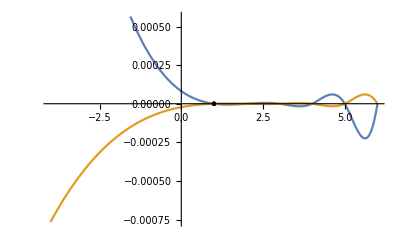

```mathematica
(* see *)
seePlot[p0,5,Last[goodValIter][[1;;2]],pyrf12[[n]]]
```

```mathematica
(* Function to find solutions for all levels of pyramid {l1,l2,l3,l4,...} or {l1} *)
(* Input-> {number of iterations, allowed failed levels, shift on v solution through levels, pixel of interests, pyrfunctions,threshold *)
(* Output-> {v1, v2,status}*)
PyrFlow1DIter[i_,n_,u_, p0_,newv0_, pyrfunctions_,threshold_,"ConstrainedNewMethod"]:=Block[{c,updateValues,newVals,tableNewValues,tValues,iterTable,goodValIter,nV},(


c=Length[pyrfunctions]; (* number of levels *)

(*{v1, v2, status, e}*)
updateValues={0.,0.,"ok",0.};

Table[

(* Flag to stop when e≥n *)
If[updateValues[[4]]<=n,updateValues[[3]]="ok", updateValues={0.,0.,updateValues[[3]],updateValues[[4]]}];

(* This will only give values that sum up to the magnitude of v 
Or if v0 = 0, list newv0 is created and fed to the function to try all it's contained values *)
nV=newValues[10,n,u,updateValues[[1;;4]],newv0,"ConstrainedNewMethod"];


tableNewValues=Table[

(* We initialize whith values calculated at nV and last calculated updateValues[[3;;4]]*)
tValues=Flatten[{v,updateValues[[3;;4]]}];


iterTable=Table[

tValues=PyrUpgrade1D[tValues,p0, pyrfunctions[[-f]],threshold*2^(-c+1),n,"ConstrainedNewMethod"]
,{j,1,i}]

,{v,nV}];

c=c-1;

goodValIter=pickNewValueIter[tableNewValues,"ConstrainedNewMethod"];
updateValues=Last[goodValIter];

goodValIter[[All,1;;3]]
,{f,1,Length[pyrfunctions]}]

)];
```

#### Test

```mathematica
Table[
PyrFlow1D[10,1,0.04,p,newv0, pyrf12[[1;;4]],0.001,noteBookMode]
,{p,1,30}]
```

{PyrFlow1D[10,1,0.04,1,{{-0.281601,-4.7184},{-0.253441,-4.24656},{-0.225281,-3.77472},{-0.197121,-3.30288},{-0.168961,-2.83104},{-0.140801,-2.3592},{-0.11264,-1.88736},{-0.0844803,-1.41552},{-0.0563202,-0.94368},67,{0.,1.5},{0.,2.},{0.,2.5},{0.,3.},{0.,3.5},{0.,4.},{0.,4.5},{0.,5.}},{{{InterpolatingFunction[…],InterpolatingFunction[…]},{InterpolatingFunction[…],InterpolatingFunction[…]}},{{InterpolatingFunction[…],InterpolatingFunction[…]},{InterpolatingFunction[…],InterpolatingFunction[…]}},{{InterpolatingFunction[…],InterpolatingFunction[…]},{InterpolatingFunction[…],InterpolatingFunction[…]}},{{InterpolatingFunction[…],InterpolatingFunction[…]},{InterpolatingFunction[…],InterpolatingFunction[…]}}},0.001,ConstrainedNewMethod],29}
 |  |  |  |

```mathematica
Table[
PyrFlow1DIter[10,1,0.04,p,newv0, pyrf12[[1;;4]],0.001,noteBookMode][[-1,-1]]
,{p,1,30}]
```

{{0.,0.,sign},{0.,0.,sign},{0.,0.,sign},{0.,0.,sign},{0.,0.,sign},{0.,0.,sign},{0.,0.,sign},{0.,0.,sign},{0.0147527,0.985247,converged},{0.0904302,0.81064,ok},{0.499996,0.500004,converged},{0.907521,0.0924791,converged},{0.00609028,0.960915,converged},{0.00254619,0.981148,converged},{0.,0.,sign},{0.983834,0.00117362,converged},{0.960915,0.00609028,converged},{0.100847,0.806055,ok},{0.500004,0.499996,converged},{0.907516,0.092484,converged},{0.00641285,0.958951,converged},{0.00641285,0.958951,converged},{0.985247,0.0147527,converged},{0.985247,0.0147526,converged},{0.,0.,mag},{0.,0.,mag},{0.,0.,mag},{0.,0.,mag},{0.,0.,mag},{0.,0.,mag}}

```mathematica
Table[
PyrFlow1D[10,1,0.02, p,newv0, pyrf12[[1;;4]],0.001,noteBookMode]==PyrFlow1DIter[10,1,0.02,p,newv0, pyrf12[[1;;4]],0.001,noteBookMode][[-1,-1]]
,{p,1,30}]
```

{1}
 |  |  |  |

#### Test

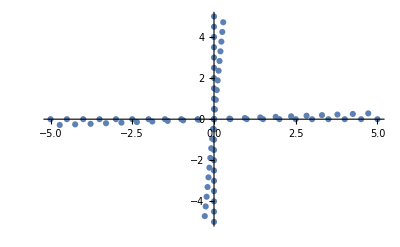

```mathematica
(* List of initial values we are going to try *)
ListPlot[newv0]
```

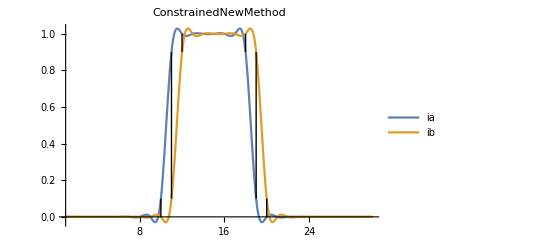

```mathematica
seeAllLine[1,0.04,newv0,Range[1,30],pyrf12[[1;;4]],0.001,noteBookMode]
```

```mathematica
(* Creating list of initial Values *)
rangev0=Range[0,5,0.5];
r=Random[];
listv0=Join[{r,1-r}*#&/@rangev0,{1-r,r}*#&/@rangev0,{1,0}*#&/@rangev0,{0,1}*#&/@rangev0,{0.5,0.5}*#&/@rangev0,{0.25,0.75}*#&/@rangev0,{0.75,0.25}*#&/@rangev0,{0.4,0.6}*#&/@rangev0,{0.6,0.4}*#&/@rangev0];
```

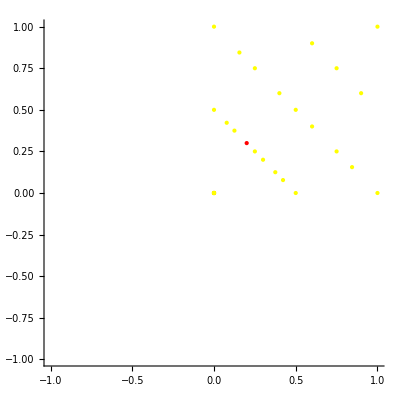
-Graphics-ConstrainedNewMethod

```mathematica
lvlmin=1;
lvlmax=3;
p=10;
dis=4;

mode="ConstrainedNewMethod";
pixelInitialValueGraphics[10,1,0.04,p,listv0,dis, pyrf12[[lvlmin;;lvlmax]],0.001*2^(-lvlmin+1),mode]
```

```mathematica
lvlmin=3;
lvlmax=3;
p=14;
mode="ConstrainedNewMethod";

(*pixelInitialValueGraphics[10,1000,p,{-10,10},dis, pyrf12[[lvlmin;;lvlmax]],0.001*2^(-lvlmin+1),mode]*)
```